Grade 100

# Lesson 6

## Mario L Gutierrez

scoring: 8 problems each worth 12 points, plus 4 free points.

## Solving Equations in one and several variables

This lesson involves a lot of reading, particularly in Wolfram’s excellently written tutorials. It is essential that you do this reading in the order it is assigned. You won’t be able to do the problems without having done the problems beforehand. As usual the tutorials are Mathematics notebooks. You can do your own examples in them without altering the notebooks.It is essential that you experiment.

Read S 6.1
Query Solve and Eliminate.

Read SolvingEquations up to Out 6.
Read EliminatingVariables.

The following section is a typical example of how we might use the Solve and Eliminate commands.

```mathematica
Clear["Global`*"]
```

## A Cartesian Treatment of the Cycloid

### Cartesian implicit equations for the cycloid: Eliminate

Recall (lesson 4) the parametric equations of the cycloid

```mathematica
eqx=x==t-Sin[t]
```

x==t-Sin[t]

```mathematica
eqy=y==1-Cos[t]
```

y==1-Cos[t]

We have two equations in three variables x,y and t we try to get Cartesian equations by eliminating t

```mathematica
elim=Eliminate[{eqx,eqy},t]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

-2 x ArcCos[1-y]+ArcCos[1-y]^2==-x^2+2 y-y^2||2 x ArcCos[1-y]+ArcCos[1-y]^2==-x^2+2 y-y^2

Let’s disregard the warning. Then we get two possible implicit Cartesian equations. Let’s name them:

```mathematica
eqelimneg=-2 x ArcCos[1-y]+ArcCos[1-y]^2==-x^2+2 y-y^2
```

-2 x ArcCos[1-y]+ArcCos[1-y]^2==-x^2+2 y-y^2

```mathematica
eqelimpos=2 x ArcCos[1-y]+ArcCos[1-y]^2==-x^2+2 y-y^2
```

2 x ArcCos[1-y]+ArcCos[1-y]^2==-x^2+2 y-y^2

### Explicit Solutions: Solve

Now since we have a bias for trying to solve for y in terms of x lets try to solve the implicit equations for y  as an explicit expression in x.

```mathematica
Solve[eqelimpos ,y,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[2 x ArcCos[1-y]+ArcCos[1-y]^2==-x^2+2 y-y^2,y,Reals]

```mathematica
Solve[eqelimneg,y,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-2 x ArcCos[1-y]+ArcCos[1-y]^2==-x^2+2 y-y^2,y,Reals]

Solve is meant primarily for polynomial equations, both of our equations involve the transcendental function ArcCos and so it is not surprising that Solve fails. We should have the same trouble trying to solve for x in terms of y but let’s try:

```mathematica
Solve[eqelimpos,x,Reals]
```

{{x→ConditionalExpression[-√(2 y-y^2)-ArcCos[1-y],0<y<2]},{x→ConditionalExpression[√(2 y-y^2)-ArcCos[1-y],0<y<2]}}

Somewhat surprisingly we get two solutions. ConditionalExpression is telling us the solutions are only valid  when 0<y<2 or so Mathematica is indicating. They actually work for 0≤x≤2

```mathematica
Solve[eqelimneg,x,Reals]
```

{{x→ConditionalExpression[-√(2 y-y^2)+ArcCos[1-y],0<y<2]},{x→ConditionalExpression[√(2 y-y^2)+ArcCos[1-y],0<y<2]}}

It is useful to notice that the solutions for eqelimneg are the negative of the solutions for eqelimpos.

Let’s plot the solutions for eqelimneg on the same graph. Since we are graphing expressions in y we will take the horizontal  axis to be y and vertical axis to be x

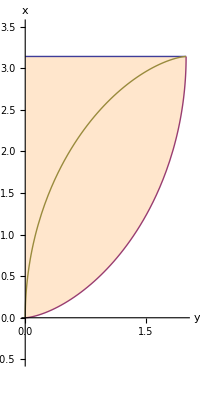

```mathematica
Plot[Tooltip[{π,-√(2 y-y^2)+ArcCos[1-y],√(2 y-y^2)+ArcCos[1-y]}],{y,0,2},AxesLabel->{"y","x"},LabelStyle->{Red},PlotRange->{-1/2,7/2},AspectRatio->Automatic,Filling->{1->{{2},LightOrange}}]
```

Note the Filling option ( S 106-107). I fiddled around with the color of the filling until I could see the curves clearly. Tooltip (R p122) comes in handy.

View the curves as lying to the right of the x-axis (remember this axis is vertical) and comparing with the ParametricPlot of the cycloid which we saw in the beginning of lesson 4, the plot of

-√(2 y-y^2)+ArcCos[1-y]

yields half a hump of the cycloid ( to the right of the x-axis).

### Areas and Arc-length of the Cycloid

#### Area

Let's find the area of this half-hump. The Filling option (S p106) shades the area that we want. We get this area by integrating  top function minus bottom function with respect to y.

```mathematica
Integrate[π-(-√(2 y-y^2)+ArcCos[1-y]),{y,0,2}]
```

(3 π)/2

The area of a half-hump is (3π)/2. Thus the area of one hump of the cycloid is 3π. This is consistent with the result we got at the beginning of lesson 4.

#### Arc-length

Remember from first year calculus that the arc-length of the plot of u=f(z) as z goes from a to b is

∫_a^b √(1+f'(z)^2)ⅆz

```mathematica
dx=D[-√(2 y-y^2)+ArcCos[1-y],y]
```

1/(√(1-(1-y)^2))-(2-2 y)/(2 √(2 y-y^2))

```mathematica
Integrate[√(1+dx^2),{y,0,2}]
```

4

Thus the arc-length of one whole hump of the cycloid is 8. This is the same answer we got in the beginning of lesson 4.

```mathematica
Clear["Global`*"]
```

## Solving Equations in One Variable:

Read the tutorial ApplyingTransformationRules down to In[14]. From our reading (SolvingEquations) we have seen that the output from the Solve command is given in terms of replacement rules. This is actually what we should prefer because most often we want to substitute our solution into other expressions. If we want the solutions we just substitute into our variable

```mathematica
Solve[x^2+3x+1==2,x]
```

{{x→1/2 (-3-√13)},{x→1/2 (-3+√13)}}

```mathematica
x/.Solve[x^2+3x+1==2,x]
```

{1/2 (-3-√13),1/2 (-3+√13)}

A peculiarity: If we Solve  an equation with one solution and substitute we get a one element list

```mathematica
Solve[3x+1==2,x]
```

{{x→1/3}}

```mathematica
x/.Solve[3x+1==2,x]
```

{1/3}

If we want to get the actual solution we have to do it with something like

```mathematica
x/.Solve[3x+1==2,x][[1]]
```

1/3

or

```mathematica
x/.Flatten[Solve[3x+1==2,x]]
```

1/3

In any Solve  the output { } mean no solutions and {{ }} means an infinite number of solutions .

```mathematica
Solve[(x-1)^2==x^2-2x+1,x]
```

{{}}

```mathematica
Solve[(x-1)^2==x^2-2x+2,x]
```

{}

#### Distance Between a Point and a Line

The equation a x+b y+c=0 is the most general form of the equation of a straight-line in the plane (one of a,b must be non-zero). Recall that multiplying a,b,c by the same non-zero constant gives an equivalent equation and hence the same line. Let p={x0,y0}  be a point in the plane. Let L0     be the line with equation a x+b y+c=0. Let L1 be the line through p and perpendicular to L0. Let q be the intersection of L0 and L1. The distance between p and L0 is by definition the distance between p and q.

Problem1  a: Write down an equation for L1.

L1=b x_0-b x+a y-a y_0==0

b: Set up and then solve exactly equations for {x1,y1}. The rule(s) you get should only have a,b,c,x0,y0 on the right hand side(s)  .  You will be using the lists of rules later so assign the list to pointrule1.

```mathematica
{x1,y1}= Solve[{a x+b y+c==0,-b x+a y-a y0+b x0==0},{x,y}]⟦1⟧
```

{x→-(a c-b^2 x0+a b y0)/(a^2+b^2),y→-(b c+a b x0-a^2 y0)/(a^2+b^2)}

```mathematica
pointrule1={x1,y1};
```

c: Use the result of b: to substitute into the expression for the distance between p and q. You should get an expressions which only involves   a,b,c,x0,y0 .

```mathematica
d=√((-(a c-b^2 x0+a b y0)/(a^2+b^2)-x0)^2+(-(b c+a b x0-a^2 y0)/(a^2+b^2)-y0)^2)
```

√((-y0-(b c+a b x0-a^2 y0)/(a^2+b^2))^2+(-x0-(a c-b^2 x0+a b y0)/(a^2+b^2))^2)

d:  Apply Simplify to this result

```mathematica
Simplify[√((-(a c-b^2 x0+a b y0)/(a^2+b^2)-x0)^2+(-(b c+a b x0-a^2 y0)/(a^2+b^2)-y0)^2)]
```

√((c+a x0+b y0)^2/(a^2+b^2))

12 points

### Root objects

Query Root. Read Equations In One Variable.
Root objects are symbolic representations of the roots of pure functions. The syntax of Root is Root[purefunction,number]. If the pure function is polynomial of degree n the numbers will run from 1 to n. The real roots come first in numerical order and then the complex roots in conjugate pairs.

```mathematica
sols=x/.Solve[x^7+x^4+2x+1==0,x]
```

{Root[1+2 #1+#1^4+#1^7&,1],Root[1+2 #1+#1^4+#1^7&,2],Root[1+2 #1+#1^4+#1^7&,3],Root[1+2 #1+#1^4+#1^7&,4],Root[1+2 #1+#1^4+#1^7&,5],Root[1+2 #1+#1^4+#1^7&,6],Root[1+2 #1+#1^4+#1^7&,7]}

```mathematica
N[sols]
```

{-0.5346,-0.903796-0.412095 ⅈ,-0.903796+0.412095 ⅈ,0.200712-1.15691 ⅈ,0.200712+1.15691 ⅈ,0.970384-0.658336 ⅈ,0.970384+0.658336 ⅈ}

In Mathematica 9 the pure function can be transcendental in which case number will be a high precision decimal and the root object is a symbolic representation of the (exact) root of the transcendental function near to the high precision number.

#### Three Points Determine a Circle

Remember the general form of a straight line which passes through (x_1,y_1) and (x_2,y_2) for distinct points  (x_1,y_1) and (x_2,y_2)

(y_2-y_1)(x-x_1)-(x_2-x_1)(y-y_1)=0

Thus if (x_3,y_3) does not lie on the line through  (x_1,y_1) and (x_2,y_2) we must have

(y_2-y_1)(x_3-x_1)-(x_2-x_1)(y_3-y_1)≠0

Using Expand on the left hand side

```mathematica
Expand[(Subscript[y, 2]-Subscript[y, 1])(Subscript[x, 3]-Subscript[x, 1])-(Subscript[x, 2]-Subscript[x, 1])(Subscript[y, 3]-Subscript[y, 1])]≠0
```

x_2 y_1-x_3 y_1-x_1 y_2+x_3 y_2+x_1 y_3-x_2 y_3≠0

Problem2 It is a theorem in geometry that any three non-collinear points determine a circle. Given  the three points {x_1,y_1},{x_2,y_2},{x_3,y_3} find a,b,and R for the circle (x-a)^2 +(y - b)^2=R that passes through them. Making a table of equations will save a lot of typing. 
 If you do this right you will notice that the solutions have the same denominator or its square. What does the equation denominator=0 signify for the three points.?

```mathematica
list=Table[(Subscript[x, i]-a)^2+(Subscript[y, i]-b)^2==R,{i,1,3}];
Solve[list,{a,b,R}]
```

{{a→(x_2^2 y_1-x_3^2 y_1-x_1^2 y_2+x_3^2 y_2-y_1^2 y_2+y_1 y_2^2+x_1^2 y_3-x_2^2 y_3+y_1^2 y_3-y_2^2 y_3-y_1 y_3^2+y_2 y_3^2)/(2 (x_2 y_1-x_3 y_1-x_1 y_2+x_3 y_2+x_1 y_3-x_2 y_3)),b→(x_1^2 x_2-x_1 x_2^2-x_1^2 x_3+x_2^2 x_3+x_1 x_3^2-x_2 x_3^2+x_2 y_1^2-x_3 y_1^2-x_1 y_2^2+x_3 y_2^2+x_1 y_3^2-x_2 y_3^2)/(2 (x_2 y_1-x_3 y_1-x_1 y_2+x_3 y_2+x_1 y_3-x_2 y_3)),R→((x_2^2-2 x_2 x_3+x_3^2+y_2^2-2 y_2 y_3+y_3^2) (x_1^4-2 x_1^3 x_2+x_1^2 x_2^2-2 x_1^3 x_3+4 x_1^2 x_2 x_3-2 x_1 x_2^2 x_3+x_1^2 x_3^2-2 x_1 x_2 x_3^2+x_2^2 x_3^2+2 x_1^2 y_1^2-2 x_1 x_2 y_1^2+x_2^2 y_1^2-2 x_1 x_3 y_1^2+x_3^2 y_1^2+y_1^4-2 x_1^2 y_1 y_2+4 x_1 x_3 y_1 y_2-2 x_3^2 y_1 y_2-2 y_1^3 y_2+x_1^2 y_2^2-2 x_1 x_3 y_2^2+x_3^2 y_2^2+y_1^2 y_2^2-2 x_1^2 y_1 y_3+4 x_1 x_2 y_1 y_3-2 x_2^2 y_1 y_3-2 y_1^3 y_3+4 y_1^2 y_2 y_3-2 y_1 y_2^2 y_3+x_1^2 y_3^2-2 x_1 x_2 y_3^2+x_2^2 y_3^2+y_1^2 y_3^2-2 y_1 y_2 y_3^2+y_2^2 y_3^2))/(4 (x_2 y_1-x_3 y_1-x_1 y_2+x_3 y_2+x_1 y_3-x_2 y_3)^2)}}

```mathematica
Denominator[(Subscript[x, 2]^2 Subscript[y, 1]-Subscript[x, 3]^2 Subscript[y, 1]-Subscript[x, 1]^2 Subscript[y, 2]+Subscript[x, 3]^2 Subscript[y, 2]-Subscript[y, 1]^2 Subscript[y, 2]+Subscript[y, 1] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 3]-Subscript[x, 2]^2 Subscript[y, 3]+Subscript[y, 1]^2 Subscript[y, 3]-Subscript[y, 2]^2 Subscript[y, 3]-Subscript[y, 1] Subscript[y, 3]^2+Subscript[y, 2] Subscript[y, 3]^2)/(2 (Subscript[x, 2] Subscript[y, 1]-Subscript[x, 3] Subscript[y, 1]-Subscript[x, 1] Subscript[y, 2]+Subscript[x, 3] Subscript[y, 2]+Subscript[x, 1] Subscript[y, 3]-Subscript[x, 2] Subscript[y, 3]))]
```

2 (x_2 y_1-x_3 y_1-x_1 y_2+x_3 y_2+x_1 y_3-x_2 y_3)

```mathematica
Denominator[(Subscript[x, 1]^2 Subscript[x, 2]-Subscript[x, 1] Subscript[x, 2]^2-Subscript[x, 1]^2 Subscript[x, 3]+Subscript[x, 2]^2 Subscript[x, 3]+Subscript[x, 1] Subscript[x, 3]^2-Subscript[x, 2] Subscript[x, 3]^2+Subscript[x, 2] Subscript[y, 1]^2-Subscript[x, 3] Subscript[y, 1]^2-Subscript[x, 1] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 3]^2-Subscript[x, 2] Subscript[y, 3]^2)/(2 (Subscript[x, 2] Subscript[y, 1]-Subscript[x, 3] Subscript[y, 1]-Subscript[x, 1] Subscript[y, 2]+Subscript[x, 3] Subscript[y, 2]+Subscript[x, 1] Subscript[y, 3]-Subscript[x, 2] Subscript[y, 3]))]
```

2 (x_2 y_1-x_3 y_1-x_1 y_2+x_3 y_2+x_1 y_3-x_2 y_3)

```mathematica
Denominator[((Subscript[x, 2]^2-2 Subscript[x, 2] Subscript[x, 3]+Subscript[x, 3]^2+Subscript[y, 2]^2-2 Subscript[y, 2] Subscript[y, 3]+Subscript[y, 3]^2) (Subscript[x, 1]^4-2 Subscript[x, 1]^3 Subscript[x, 2]+Subscript[x, 1]^2 Subscript[x, 2]^2-2 Subscript[x, 1]^3 Subscript[x, 3]+4 Subscript[x, 1]^2 Subscript[x, 2] Subscript[x, 3]-2 Subscript[x, 1] Subscript[x, 2]^2 Subscript[x, 3]+Subscript[x, 1]^2 Subscript[x, 3]^2-2 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3]^2+Subscript[x, 2]^2 Subscript[x, 3]^2+2 Subscript[x, 1]^2 Subscript[y, 1]^2-2 Subscript[x, 1] Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^2-2 Subscript[x, 1] Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^2+Subscript[y, 1]^4-2 Subscript[x, 1]^2 Subscript[y, 1] Subscript[y, 2]+4 Subscript[x, 1] Subscript[x, 3] Subscript[y, 1] Subscript[y, 2]-2 Subscript[x, 3]^2 Subscript[y, 1] Subscript[y, 2]-2 Subscript[y, 1]^3 Subscript[y, 2]+Subscript[x, 1]^2 Subscript[y, 2]^2-2 Subscript[x, 1] Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^2+Subscript[y, 1]^2 Subscript[y, 2]^2-2 Subscript[x, 1]^2 Subscript[y, 1] Subscript[y, 3]+4 Subscript[x, 1] Subscript[x, 2] Subscript[y, 1] Subscript[y, 3]-2 Subscript[x, 2]^2 Subscript[y, 1] Subscript[y, 3]-2 Subscript[y, 1]^3 Subscript[y, 3]+4 Subscript[y, 1]^2 Subscript[y, 2] Subscript[y, 3]-2 Subscript[y, 1] Subscript[y, 2]^2 Subscript[y, 3]+Subscript[x, 1]^2 Subscript[y, 3]^2-2 Subscript[x, 1] Subscript[x, 2] Subscript[y, 3]^2+Subscript[x, 2]^2 Subscript[y, 3]^2+Subscript[y, 1]^2 Subscript[y, 3]^2-2 Subscript[y, 1] Subscript[y, 2] Subscript[y, 3]^2+Subscript[y, 2]^2 Subscript[y, 3]^2))/(4 (Subscript[x, 2] Subscript[y, 1]-Subscript[x, 3] Subscript[y, 1]-Subscript[x, 1] Subscript[y, 2]+Subscript[x, 3] Subscript[y, 2]+Subscript[x, 1] Subscript[y, 3]-Subscript[x, 2] Subscript[y, 3])^2)]
```

4 (x_2 y_1-x_3 y_1-x_1 y_2+x_3 y_2+x_1 y_3-x_2 y_3)^2

The denominator of a and b is same, and the denominator of R is a’s times b’s. So the three points are not on the same line. Had the denominator of these points been equal to zero, it would signify that these points are not solutions of the equation, therefore they would be collinear.

12 points

```mathematica
Clear["Global`*"]
```

### Osculating Circles and Evolutes

Query Dt and read Total Derivatives.

We have seen that three non-collinear points determine a circle.   We can also determine a circle (u-a)^2+(v-b)^2=R by giving a point (u_0,v_0) on the circle, the slope of the tangent line dv/du=d1 at (u_0,v_0)  and the second derivative (d^2  u)/(d v^2)=d2≠0 at (u_0,v_0).

Start with the equation of the circle:

```mathematica
eqcirc=(u-a)^2+(v-b)^2==R
```

(-a+u)^2+(-b+v)^2==R

Where u and v are variables and a,b, and R are the constants that determine the circle.

Now get the equation eq0 that expresses the fact that (u_0,v_0) lies on the circle.

```mathematica
eq0=eqcirc/.{u->Subscript[u, 0],v->Subscript[v, 0]}
```

(-a+u_0)^2+(-b+v_0)^2==R

Take the total derivative Dt[eqcirc,u,Constants→{a,b,R}] of the equation eqcirc with respect to u with a,b, and R taken to be constants and get an equation eq1  that expresses the facts that (u_0,v_0) lie on the circle and that  dv/du=d_1 at (u_o,v_0)  by making  the substitutions u→u_0,v→v_0  and Dt[u,v,Constants→{a,b,R}]→d_1.

```mathematica
eq1=Dt[eqcirc,u,Constants->{a,b,R}]/.{u->Subscript[u, 0],v->Subscript[v, 0],Dt[v,u,Constants->{a,b,R}]->d1}
```

2 (-a+u_0)+2 d1 (-b+v_0)==0

Now take the second total derivative Dt[eqcirc,{u,2},Constants→{a,b,R}] of the equation eqcirc with respect to u with a,b, and R taken to be constants and get an equation eq2  that expresses the facts that (u_0,v_o) lie on the circle, that  dv/du=d1 at (u_o,v_0) , and that (d^2  u)/(d v^2)=d1 by making  the substitutions u→u_0,v→v_0 , Dt[u,v,Constants→{a,b,R}]→d_1, and Dt[u,{v,2},Constants→{a,b,R}]→d_2

```mathematica
eq2=Dt[eqcirc,{u,2},Constants->{a,b,R}]/.{u->Subscript[u, 0],v->Subscript[v, 0],Dt[v,u,Constants->{a,b,R}]->d1,Dt[v,{u,2},Constants->{a,b,R}]->d2}
```

2+2 d1^2+2 d2 (-b+v_0)==0

Now we solve these equations for a,b, and R.

```mathematica
sols=Solve[{eq0,eq1,eq2},{a,b,R}]
```

{{a→(-d1-d1^3+d2 u_0)/d2,b→(1+d1^2+d2 v_0)/d2,R→((1+d1^2)^3)/d2^2}}

Since we are dealing with a circle and its tangent line we expect that the line from (a,b) to (u_0,v_0)  should be perpendicular to the tangent line i.e. their slopes should be negative reciprocal

```mathematica
(b-Subscript[v, 0])/(a-Subscript[u, 0])/.sols
```

{(-v_0+(1+d1^2+d2 v_0)/d2)/(-u_0+(-d1-d1^3+d2 u_0)/d2)}

```mathematica
Simplify[%]
```

{-1/d1}

The curvature of a circle of radius r is 1/r  . In this case the curvature is

1/(√(((1+d_1^2)^3)/d_2^2))

The point (a,b) is called the center of curvature. 

Now suppose that (u_0,v_0)=(x,y) and that (x,y) lies on a curve C. Let d1=dy/dx and d2=(d^2 y)/dx^2then  the circle is called the osculating circle to C at (x,y). Osculate is the Latin verb for kiss.  As (x,y) varies along C the center of curvature varies along another curve called the evolute of C. We examine two cases:

y=f(x) (explicit case)

More generally:

x=x(t),y=y(t) (parametrized case)

#### The explicit Case: y=f(x).

Then we have d1=f'(x) and d2=f''(x). At a general point (x,f(x)) on the curve we have

```mathematica
Clear[f]
```

```mathematica
a[x_]:=(-f'[x]-f'[x]^3+f''[x] x)/f''[x]
```

```mathematica
b[x_]:=(1+f'[x]^2+f''[x] f[x])/f''[x]
```

```mathematica
R[x_]:=((1+f'[x]^2)^3)/f''[x]^2
```

We denote the curvature at (x,f(x)) by κ(x).

```mathematica
κ[x_]:=1/(√R[x])
```

Just as we can think of the graph of a function, f(x) as a parametrized curve parametrized by x, the evolute, which in general is not the graph of a function is a parametrized curve with parameter x, ev(x)=(a(x),b(x))

Example: The upper half of the ellipse x^2/5^2+y^2/2^2=1, y=2 √(1-x^2/5^2)

```mathematica
f[x_]:=2 √(1-x^2/5^2)
```

Let’s see the upper half of the ellipse and its evolute.

Power::infy: Infinite expression 1/0.^3/2 encountered.

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

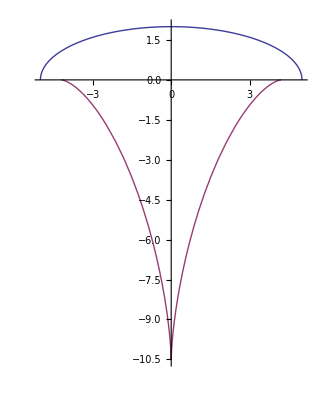

```mathematica
above=ParametricPlot[Evaluate[{{t,f[t]},{a[t],b[t]}}],{t,-5,5}]
```

The orange warnings are because of what happens at the points (-5,0) and (5,0) where the tangents are vertical

Let’s see the lower half of the ellipse and it’s evolute for -5<u<5

```mathematica
f[u_]:=-2 √(1-u^2/5^2)
```

Power::infy: Infinite expression 1/0.^3/2 encountered.

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

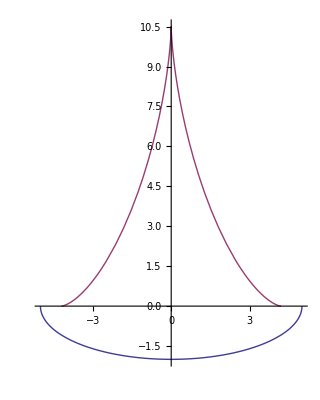

```mathematica
below=ParametricPlot[Evaluate[{{t,f[t]},{a[t],b[t]}}],{t,-5,5}]
```

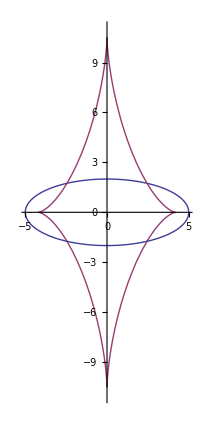

```mathematica
ellipseevolute=Show[above,below,PlotRange->{-11,11}]
```

Another Example: The evolute of the parabola x=y^2,

```mathematica
f[z_]:=z^2
```

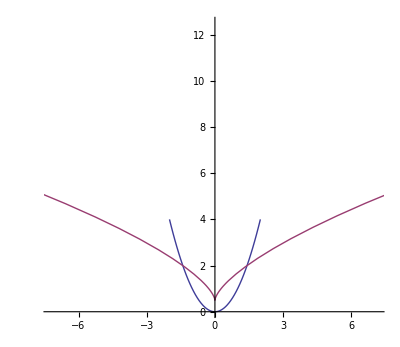

```mathematica
ParametricPlot[Evaluate[{{x,f[x]},{a[x],b[x]}}],{x,-2,2}]
```

```mathematica
f[z_]:=z^3
```

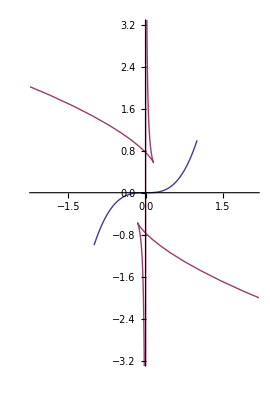

```mathematica
ParametricPlot[Evaluate[{{x,f[x]},{a[x],b[x]}}],{x,-1,1}]
```

```mathematica
Clear[f]
```

Notice here that as x→0 the second derivative goes to 0 and the radius of the osculating circle goes to ∞ and we get the vertical asymptotes on the evolute

#### The general parametrized case:

u=u(t) and v=v(t). at (u(t),v(t)) we have

d1[t]=dv/du=(dv/dt)/(du/dt)=v'[t]/u'[t]

d2[t]=(d^2 v)/(d,u^2)=((d dv/du)/dt)/(du/dt)=((d(dv/dt)/(du/dt))/dt)/(du/dt)=(((d^2 v)/dt^2 du/dt-dv/dt(d^2 u)/dt^2)/(du/dt)^2)/(du/dt)=(v''[t]u'[t]-v'[t]u''[t])/u'[t]^3

```mathematica
d1[t_]:=v'[t]/u'[t]
```

```mathematica
d2[t_]:=(v''[t]u'[t]-v'[t]u''[t])/u'[t]^3
```

```mathematica
a[t_]:=(-d1[t]-d1[t]^3+d2[t]u[t])/d2[t]
```

```mathematica
b[t_]:=(1+d1[t]^2+d2[t]v[t])/d2[t]
```

```mathematica
R[t_]:=1/(√(((1+d1[t]^2)^3)/d2[t]^2))
```

As for curvature we have

```mathematica
κ[t_]:=1/(√(((1+d1[t]^2)^3)/d2[t]^2))
```

Let’s see that we get results consistent with those we got for the ellipse

u^2/5^2+v^2/2^2=1

We parametrize this ellipse by

```mathematica
u[t_]:=5 Cos[t]
```

```mathematica
v[t_]:=2 Sin[t]
```

Now we look at the ParametricPlot of the ellipse and its evolute.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 1 + ComplexInfinity + ComplexInfinity encountered.

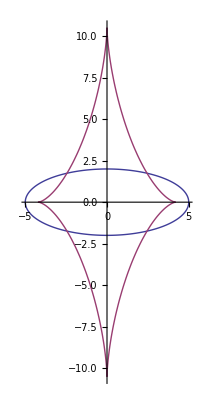

```mathematica
ParametricPlot[Evaluate[{{u[t],v[t]},{a[t],b[t]}}],{t,0,2π}]
```

Problem3:

Go back to problem set 4 and get the parametrizations of the cardioid as a hypotrochoid and as an epitrochoid.

```mathematica
d1hypo[t_]:=vhypo'[t]/uhypo'[t]
d2hypo[t_]:=(vhypo''[t]uhypo'[t]-vhypo'[t]uhypo''[t])/uhypo'[t]^3
ahypo[t_]:=(-d1hypo[t]-d1hypo[t]^3+d2hypo[t]uhypo[t])/d2hypo[t]
bhypo[t_]:=(1+d1hypo[t]^2+d2hypo[t]vhypo[t])/d2hypo[t]
```

a:Plot the cardioid and its evolute using the hypotrochoid parametrization.

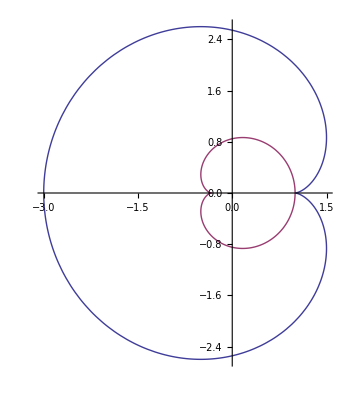

```mathematica
uhypo[t_]:=(1-2) Cos[t]+2 Cos[(1/2-1)t]
vhypo[t_]:=(1-2)Sin[t]-2 Sin[(1/2-1)t]
ParametricPlot[Evaluate[{{uhypo[t],vhypo[t]},{ahypo[t],bhypo[t]}}],{t,0,4 π}]
```

b: Plot the cardioid and its evolute using the epitrochoid parametrization. Do you get the same pairs of curves?

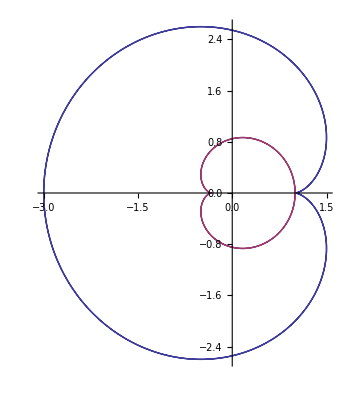

```mathematica
uepi[t_]:=(1+1) Cos[t]-1 Cos[(1/1+1)t]
vepi[t_]:=(1+1) Sin[t]-1 Sin[(1/1+1)t]
d1epi[t_]:=vepi'[t]/uepi'[t]
d2epi[t_]:=(vepi''[t]uepi'[t]-vepi'[t]uepi''[t])/uepi'[t]^3
aepi[t_]:=(-d1epi[t]-d1epi[t]^3+d2epi[t]uepi[t])/d2epi[t]
bepi[t_]:=(1+d1epi[t]^2+d2epi[t]vepi[t])/d2epi[t]
ParametricPlot[Evaluate[{{uepi[t],vepi[t]},{aepi[t],bepi[t]}}],{t,0,4 π}]
```

We do get the same pair of curves.

c: Plot the cycloid and its evolute over the interval (0,6π)

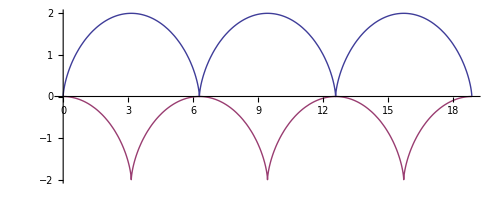

```mathematica
d1cyc[t_]:=vcyc'[t]/ucyc'[t]
d2cyc[t_]:=(vcyc''[t]ucyc'[t]-vcyc'[t]ucyc''[t])/ucyc'[t]^3
acyc[t_]:=(-d1cyc[t]-d1cyc[t]^3+d2cyc[t]ucyc[t])/d2cyc[t]
bcyc[t_]:=(1+d1cyc[t]^2+d2cyc[t]vcyc[t])/d2cyc[t]
ucyc[t_]:=t- Sin[t]
vcyc[t_]:=1-Cos[t]
ParametricPlot[Evaluate[{{ucyc[t],vcyc[t]},{acyc[t],bcyc[t]}}],{t,0,6 π}]
```

12 points

A good student would experiment in their sketch file with the evolutes of various hypotrochoids and epitrochoids. It turns out that the epitrochoids and hypotrochoids are similar ( in the geometric sense) to their evolutes.

## General Systems of Equations and Inequalities

Read: Logical Combinations of Equalities.

A general system of equations and inequalities is a sequence of equalities and inequalities with connectives && (and) or || (or). In versions of Mathematica prior to Mathematica 8 only Reduce could handle general systems. In Mathematica 9 both Reduce and Solve can handle such systems.

#### Solve and non-polynomial systems of equations:

```mathematica
exptrig[x_]:=ⅇ^x Cos[x]+ⅇ^x Sin[x]
```

```mathematica
Solve[exptrig[x]==2,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^x Cos[x]+ⅇ^x Sin[x]==2,x]

This is not surprising because exptrig  is transcendental

Many transcendental equations for which Solve fails, can be successfully done with Solve when restricted to an interval.

```mathematica
sol=x/.Solve[exptrig[x]==2&&-3/4<x<9/4,x]
```

{Root[{-2+ⅇ^#1 Cos[#1]+ⅇ^#1 Sin[#1]&,0.41629680247115649482}],Root[{-2+ⅇ^#1 Cos[#1]+ⅇ^#1 Sin[#1]&,2.1986290131592793055}]}

The general system does have solutions and they are exact:

```mathematica
Precision[sol[[1]]]
```

∞

```mathematica
Precision[sol[[2]]]
```

∞

```mathematica
N[sol]
```

{0.416297,2.19863}

```mathematica
x/.NSolve[{exptrig[x]==2,-3/4<x<9/4},x]
```

{0.416297,2.19863}

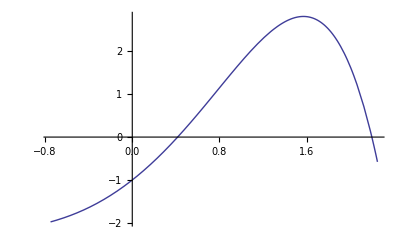

```mathematica
Plot[exptrig[x]-2,{x,-3/4,9/4}]
```

### Solve and Reduce

#### General Systems of Inequalities

Suppose we want to solve a general system of inequalities

```mathematica
Solve[x^2-9>0 &&(x-2)-5<1 || 1<x-27<2,x]
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}

We get a warning message. A Full dimensional solution in the one variable case is a solution that contain an open interval. In the n-variable case it is a solution that contains an open n-disk

```mathematica
Reduce[x^2-9>0 &&(x-2)-5<1 || 1<x-27<2,x]
```

x<-3||3<x<8||28<x<29

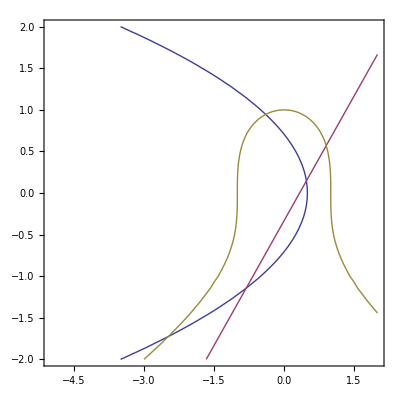

```mathematica
ContourPlot[{x+y^2==1/2,x-y==1/3,x^2+y^3==1},{x,-5,2},{y,-2,2}]
```

Query RegionPlot

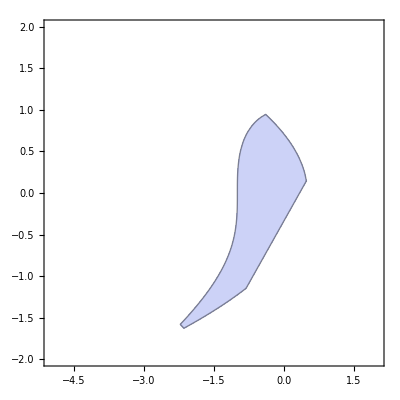

```mathematica
RegionPlot[x+y^2≤1/2&& x-y≤1/3&&x^2+y^3<1,{x,-5,2},{y,-2,2}]
```

```mathematica
Reduce[x+y^2≤1/2&& x-y≤1/3&&x^2+y^3<1,{x,y}]
```

(Root[7+6 #1-28 #1^2+8 #1^3+8 #1^4&,1]<x≤1/6 (-1-√15)&&-(√(1-2 x))/(√2)≤y<Root[-1+x^2+#1^3&,1])||(1/6 (-1-√15)<x≤Root[7+6 #1-28 #1^2+8 #1^3+8 #1^4&,2]&&1/3 (-1+3 x)≤y<Root[-1+x^2+#1^3&,1])||(Root[7+6 #1-28 #1^2+8 #1^3+8 #1^4&,2]<x<1/6 (-1+√15)&&1/3 (-1+3 x)≤y≤(√(1-2 x))/(√2))||(x==1/6 (-1+√15)&&y==1/3 (-1+1/2 (-1+√15)))

#### Reduce and Parametrized Solutions

We have seen that most Transcendental equations cannot be solved by Solve,NSolve or Reduce. Read S. example 10 and problems 6.6 and 6.7. In Mathematica 8 for transcendental equations with parametrized solutions  that is the output from Reduce contains C[1],C[2]...C[n] we can use Solve on an interval to find all solutions in that interval.

```mathematica
Solve[Sin[x]+Cos[3x]+1/2==Sin[2x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→ArcCos[Root[-3+4 #1+24 #1^2-80 #1^4+64 #1^6&,1]]},{x→ArcCos[Root[-3+4 #1+24 #1^2-80 #1^4+64 #1^6&,2]]},{x→-ArcCos[Root[-3+4 #1+24 #1^2-80 #1^4+64 #1^6&,3]]},{x→ArcCos[Root[-3+4 #1+24 #1^2-80 #1^4+64 #1^6&,4]]},{x→-ArcCos[Root[-3+4 #1+24 #1^2-80 #1^4+64 #1^6&,5]]},{x→-ArcCos[Root[-3+4 #1+24 #1^2-80 #1^4+64 #1^6&,6]]}}

```mathematica
NSolve[Sin[x]+Cos[3x]+1/2==Sin[2x],x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-1.99752-0.28296 ⅈ},{x→-1.99752+0.28296 ⅈ},{x→-0.81628},{x→0.567388},{x→1.24167},{x→3.00227}}

```mathematica
Reduce[Sin[x]+Cos[3x]+1/2==Sin[2x],x]
```

C[1]∈Integers&&(x==2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,1]]+2 π C[1]||x==2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,2]]+2 π C[1]||x==2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,3]]+2 π C[1]||x==2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,4]]+2 π C[1]||x==2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,5]]+2 π C[1]||x==2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,6]]+2 π C[1])

But if we use a system that asks for the solutions contained in an interval Solve will give complete answers

```mathematica
Solve[Sin[x]+Cos[3x]+1/2==Sin[2x]&&-8<x<15,x]
```

{{x→2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,1]]},{x→-2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,1]]},{x→2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,1]]},{x→4 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,1]]},{x→2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,2]]},{x→-2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,2]]},{x→2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,2]]},{x→4 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,2]]},{x→2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,3]]},{x→-2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,3]]},{x→2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,3]]},{x→4 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,3]]},{x→2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,4]]},{x→-2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,4]]},{x→2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,4]]}}

```mathematica
NSolve[Sin[x]+Cos[3x]+1/2==Sin[2x]&&-8<x<15,x]
```

{{x→-7.09947},{x→-5.7158},{x→-5.04152},{x→-3.28091},{x→-0.81628},{x→0.567388},{x→1.24167},{x→3.00227},{x→5.46691},{x→6.85057},{x→7.52485},{x→9.28546},{x→11.7501},{x→13.1338},{x→13.808}}

```mathematica
Reduce[Sin[x]+Cos[3x]+1/2==Sin[2x]&&-8<x<15,x]
```

x==2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,1]]||x==-2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,1]]||x==2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,1]]||x==4 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,1]]||x==2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,2]]||x==-2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,2]]||x==2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,2]]||x==4 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,2]]||x==2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,3]]||x==-2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,3]]||x==2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,3]]||x==4 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,3]]||x==2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,4]]||x==-2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,4]]||x==2 π+2 ArcTan[Root[-3+4 #1+27 #1^2-8 #1^3-33 #1^4-12 #1^5+#1^6&,4]]

```mathematica
N[%]
```

x==-0.81628||x==-7.09947||x==5.46691||x==11.7501||x==0.567388||x==-5.7158||x==6.85057||x==13.1338||x==1.24167||x==-5.04152||x==7.52485||x==13.808||x==3.00227||x==-3.28091||x==9.28546

Solve has the slight virtue of giving the solutions in order. It also gives the solutions as rules so that they can be substituted into other expressions. But, query ToRules.

Problem4: Go back and use Solve to do problem 2 of lesson 4. That is: Show that there are 11 solutions to the equation 2cos^2(2x)-Sin(x/2)=1 in the interval [0,3π]. This problem is subtler than it looks

```mathematica
exp1=2 Cos[2x]^2-Sin[x/2];
```

```mathematica
Solve[exp1==1 && 0≤x≤3π,x]
Length[%]
```

{{x→π},{x→π},{x→(7 π)/3},{x→4 π+4 ArcTan[Root[1-12 #1+3 #1^2+40 #1^3+3 #1^4-12 #1^5+#1^6&,1]]},{x→4 ArcTan[Root[1-12 #1+3 #1^2+40 #1^3+3 #1^4-12 #1^5+#1^6&,3]]},{x→4 ArcTan[Root[1-12 #1+3 #1^2+40 #1^3+3 #1^4-12 #1^5+#1^6&,4]]},{x→4 ArcTan[Root[1-12 #1+3 #1^2+40 #1^3+3 #1^4-12 #1^5+#1^6&,5]]},{x→4 ArcTan[Root[1-12 #1+3 #1^2+40 #1^3+3 #1^4-12 #1^5+#1^6&,6]]},{x→4 π+4 ArcTan[Root[1+8 #1-13 #1^2-48 #1^3-13 #1^4+8 #1^5+#1^6&,1]]},{x→4 π+4 ArcTan[Root[1+8 #1-13 #1^2-48 #1^3-13 #1^4+8 #1^5+#1^6&,2]]},{x→4 ArcTan[Root[1+8 #1-13 #1^2-48 #1^3-13 #1^4+8 #1^5+#1^6&,5]]},{x→4 ArcTan[Root[1+8 #1-13 #1^2-48 #1^3-13 #1^4+8 #1^5+#1^6&,6]]}}

12

I’ve got 12 solutions because Mathematica counts roots with multiplicity and π is a double root. Hence we actually have 11 unique solutions to our equation.

12 points

### FindRoot

Query FindRoot. Read S 6.2. You may skip examples 20 and 21 but you should pay particular attention to problem 23. FindRoot  has two purposes: The first is to solve systems of equations that involve transcendental functions and the second is to find a numerical solution of a system of equations that lie near a given point. When we use Solve we need to guess an interval or region in which the roots lie and this may sometimes be difficult.

Problem5 An horizontal steel rod 1 mile long, at ground level, and pinned at its ends is heated, expands by 1 foot, and bows up into a circular arc. How high is the center of the circular are above the ground. The following diagram may help. As you will see later the diagram is very not to scale.

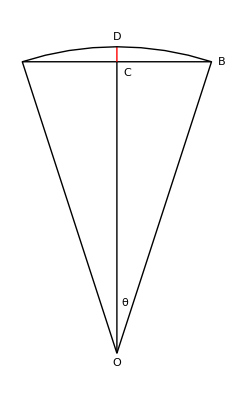

You may wish to approach the problem is the following fashion: In feet what are the length of the segment CB and the arc DB. Let the length of the segment OB be r. Now We wish to find out the length of the segment CD. What is the length of CB as a function of r and θ?. What is the length of the arc as a function of r and θ. You get a system of two equations in r and θ. Use FindRoot to solve this system of equations. Now write the length of CD in terms of r and θ and substitute your solution for r and θ.

```mathematica
sol= FindRoot[{Sin[θ] r==2640&&2 θ r==5281},{r,1},{θ,1}]
r - r Cos[θ] /. sol
```

{r→78335.1,θ→0.0337078}

44.4985

12 points

Problem6 Using a graphics object reproduce the diagram above. Hint chose θ=π/2.5,r=3. Hint: The big triangle is a  line primitive with 4 points. OC and OB are line primitives. The arc is a  Circle primitive with all three of its arguments, Then you have a bunch of text primitives. You can build the diagram out of several Graphics objects using Show. Or you can build it out of one graphics object.

0.14683

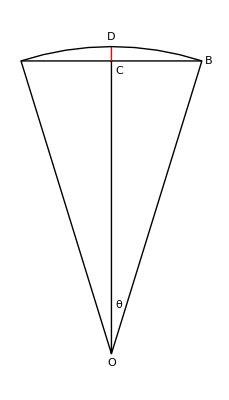

```mathematica
r = 3;
θ =(π/2-π/2.5);
CB = r Sin[θ];
OC = r Cos[θ];
OB = r;
h = OB - OC
Show[Graphics[{Line[{{0,0},{-CB,OB},{CB,OB},{0,0},{0,OB}}], Directive [Red],Line[{{0,OB},{0,OB+h}}],Black,Circle[{0,h},3,{π/2.5,(π/2)+θ}],Text["O",{0,-.1}],Text["θ",{.075,.5}],Text["C",{.075,2.90}],Text["B",{1,3}],Text["D",{0,3.25}]}]]
```

Building a graphic out of parts using Show is easier.

12 points

## Domains

Mathematica has 5 domains Integers,Rationals,Reals,and Complexes. It also has a domain Algebraics. A number is algebraic if it is a root of a polynomial with integer coefficients. We have a predicate ∈ which tells us whether a number is in the domain

```mathematica
5∈Integers
```

True

```mathematica
sols=x/.Solve[4/5 x^17+3 x^4+2==3/4 x^5+x^7,x]
```

{Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,1],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,2],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,3],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,4],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,5],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,6],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,7],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,8],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,9],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,10],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,11],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,12],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,13],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,14],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,15],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,16],Root[40+60 #1^4-15 #1^5-20 #1^7+16 #1^17&,17]}

Notice by definition all of these solutions are algebraic.

```mathematica
Clear[sols]
```

Coordinates of solutions of systems of algebraic equations in several variables are also algebraic:

```mathematica
sols={x,y}/.Solve[{x^5 +3 x^2 y^2+x+y==27,x^8 y+y^17+x-2==0},{x,y}]
```

{{(«1»)/(9668531601446180663810682«299»5846538946758321590978620),Root[-7+12699 #1+«88»+24 #1^72+#1^85&,1]},«83»,{(«1»)/(«348»0),«1»}}

{(«1»)/(966853160144618066381068236«295»395846538946758321590978620),Root[-7+12699 #1+109605 #1^2+«87»+24 #1^72+#1^85&,2]}

```mathematica
Length[sols]
```

85

```mathematica
sols[[78,1]]∈Algebraics
```

True

```mathematica
sols[[78,2]]∈Algebraics
```

True

A non-algebraic number is called transcendental. See transcendental numbers.

```mathematica
π∈Algebraics
```

False

```mathematica
ⅇ∈ Algebraics
```

False

Both of these are profound facts.

```mathematica
(ⅇ+π)∈ Algebraics
```

ⅇ+π∈Algebraics

Mathematica does not know whether ⅇ+π is algebraic and for that matter no mathematician knows either. But it is a theorem that at least one of ⅇ+π or ⅇ π is transcendental but this fact is not known to Mathematica.

```mathematica
(ⅇ+π)∈Algebraics||ⅇ π∈Algebraics
```

ⅇ+π∈Algebraics||ⅇ π∈Algebraics

It would be surprising if either of e+π or ⅇ π was transcendental.

### Reduce and Domains

```mathematica
?Reduce
```

Query Reduce and read Equations and Inequalities Over Domains. In Mathematica 8 we can also use Solve with domains.

Problem7: Consider the function

```mathematica
f[c_]:=y^2-2 x^2(x+3)==c((y+1)^2(y+9)-x^2)
```

Which we saw in problem 3 lesson 4.

a: Let c1 and c2 be two distinct exact numbers.Use -ⅇ and π. Are all the solutions to the system {f[c1],f[c2]} real? Hint: Use Length to count the number of real solutions and Length to count the number of complex solutions. Are these two integers the same. Are all the solutions algebraic?

```mathematica
f[c_]:=y^2-2 x^2 (x+3) ==c((y+1)^2 (y+9)-x^2)
Length[Solve[{f[-ⅇ],f[π]},{x,y},Reals]]
```

7

```mathematica
Length[Solve[{f[-ⅇ],f[π]},{x,y},Complexes]]
```

9

No, all the solutions to the system {f[c1],f[c2]} where c1 = -ⅇ and c2 = π are not real.  Since we know that every Real number is also a Complex number and above we can see that the lengths of the two lists above are not equal, we can say that all the solutions to the system are not real.  There are two solutions that aren’t real.  However, from our analysis below we see that all solutions are algebraic.  That turns out just as expected since all Algebraics are known to comprise all Complex numbers as well. vice versa Algebraics⊂Complexes

```mathematica
Length[Solve[{f[-ⅇ],f[π]},{x,y},Algebraics]]
```

9

```mathematica
Length[Solve[{f[-ⅇ],f[π]},{x,y},Complexes]]
```

9

12 points

#### Pythagorean Triples

A Pythagorean triple is a triple of positive integers {x,y,z} with x^2+y^2=z^2

Problem8

a: Give all the Pythagorean triples with 0<x<y <z<100. Give your result as a Column of triples

```mathematica
Solve[{x^2+y^2==z^2,0<x<y<z<100},{x,y,z},Integers]
```

{{x→3,y→4,z→5},{x→5,y→12,z→13},{x→7,y→24,z→25},{x→8,y→15,z→17},{x→9,y→12,z→15},{x→9,y→40,z→41},{x→11,y→60,z→61},{x→12,y→35,z→37},{x→13,y→84,z→85},{x→15,y→20,z→25},{x→15,y→36,z→39},{x→16,y→63,z→65},{x→20,y→21,z→29},{x→21,y→28,z→35},{x→21,y→72,z→75},{x→24,y→45,z→51},{x→25,y→60,z→65},{x→27,y→36,z→45},{x→28,y→45,z→53},{x→33,y→44,z→55},{x→33,y→56,z→65},{x→35,y→84,z→91},{x→36,y→77,z→85},{x→39,y→52,z→65},{x→39,y→80,z→89},{x→40,y→75,z→85},{x→45,y→60,z→75},{x→48,y→55,z→73},{x→51,y→68,z→85},{x→57,y→76,z→95},{x→60,y→63,z→87},{x→65,y→72,z→97},{x→6,y→8,z→10},{x→10,y→24,z→26},{x→12,y→16,z→20},{x→14,y→48,z→50},{x→16,y→30,z→34},{x→18,y→24,z→30},{x→18,y→80,z→82},{x→20,y→48,z→52},{x→24,y→32,z→40},{x→24,y→70,z→74},{x→30,y→40,z→50},{x→30,y→72,z→78},{x→32,y→60,z→68},{x→36,y→48,z→60},{x→40,y→42,z→58},{x→42,y→56,z→70},{x→48,y→64,z→80},{x→54,y→72,z→90}}

b: Some of the triples are redundant in that we get them by simply multiplying each element in the triple by a common integer. Get the column of triples that have no common integer divisors. Hint use GCD

```mathematica
Solve[{x^2+y^2==z^2,GCD[x,y,z]==1,0<x<y<z<100},{x,y,z},Integers]
```

{{x→3,y→4,z→5},{x→5,y→12,z→13},{x→7,y→24,z→25},{x→8,y→15,z→17},{x→9,y→40,z→41},{x→11,y→60,z→61},{x→12,y→35,z→37},{x→13,y→84,z→85},{x→16,y→63,z→65},{x→20,y→21,z→29},{x→28,y→45,z→53},{x→33,y→56,z→65},{x→36,y→77,z→85},{x→39,y→80,z→89},{x→48,y→55,z→73},{x→65,y→72,z→97}}

d: We see a few such triples with z=y+1. Find all such triples with z<1000. Surprisingly although it is redundant the GCD condition must be left in.

```mathematica
Solve[{x^2+y^2==z^2,z==1+y,GCD[x,y,z]==1,z<1000},{x,y,z},Integers]
```

{{x→-43,y→924,z→925},{x→-41,y→840,z→841},{x→-39,y→760,z→761},{x→-37,y→684,z→685},{x→-35,y→612,z→613},{x→-33,y→544,z→545},{x→-31,y→480,z→481},{x→-29,y→420,z→421},{x→-27,y→364,z→365},{x→-25,y→312,z→313},{x→-23,y→264,z→265},{x→-21,y→220,z→221},{x→-19,y→180,z→181},{x→-17,y→144,z→145},{x→-15,y→112,z→113},{x→-13,y→84,z→85},{x→-11,y→60,z→61},{x→-9,y→40,z→41},{x→-7,y→24,z→25},{x→-5,y→12,z→13},{x→-3,y→4,z→5},{x→-1,y→0,z→1},{x→1,y→0,z→1},{x→3,y→4,z→5},{x→5,y→12,z→13},{x→7,y→24,z→25},{x→9,y→40,z→41},{x→11,y→60,z→61},{x→13,y→84,z→85},{x→15,y→112,z→113},{x→17,y→144,z→145},{x→19,y→180,z→181},{x→21,y→220,z→221},{x→23,y→264,z→265},{x→25,y→312,z→313},{x→27,y→364,z→365},{x→29,y→420,z→421},{x→31,y→480,z→481},{x→33,y→544,z→545},{x→35,y→612,z→613},{x→37,y→684,z→685},{x→39,y→760,z→761},{x→41,y→840,z→841},{x→43,y→924,z→925}}

12 points